# Package of 2-D Light Tracking

## Notes

## Brief Description

This package enables a quick and interactive design and implementation of 2-D ideal optical operations.

The default package include mainly FOUR parts:

	1. Light Tracking
	2. Hardware Visualizing
	3. Light Beam Visualizing
	4. User Interface

For optical hardware, the package include the following:

	1. Light source
		1.1 Point light source
		1.2 Line light source
	2. Lens & Mirror
		2.1 Simple lens
		2.2 Complex lens with different f left and f right, non-symmetrical lens. 
		2.3 Simple mirror
		2.4 Simple mirror with non planar surface
		2.5 Complex non-symmetrical mirror
	3. Other optical operations
		3.1 Traverse
		3.2 Aperture
	4. Marker
	
These operations follow a uniform form when defining, make them easy to augment and also dev-friendly.

For visualization, the package include three forms of drawing:

	1. Lit region drawing, in some occasions capable of showing exact light flux.
	2. Boundary light beam drawing.
	3. Characteristic light beam drawing.
	
The latter two are embedded with the ability to show REAL and IMAGINARY images.
These operations follow a uniform form when defining, make them easy to augment and also dev-friendly.

For user interface, there’s mainly two parts:

	1. input interface
	2. result processing interface

## Notes For Users

### Basic Usage

First thing first, click “Evaluation” -> “Evaluate Initialization Cells” in the menu bar to initialize all functions.

For non-Mathematica users, then run this piece of code: 
	dynamicinput[]

Input your directions in a list or a nested list where contents are each of your optical hardware.

Note that you can use the floating window to help you input what you want so that you don’t need to remember everything.

Well, then follow the steps to customize your own optical system.

### Additional Notes

You can open the input helper using:
	openhelper[]

You can type your own code in a cell and run with:
	completedraw[]

If you are still not satisfied with this level of customization, you can add stuffs inside the “Small Tools” section.
Once properly defined, you can use them everywhere, inside interactive content or not.

Or if you want to adjust some features:

	Visualize hardware using
		drawhw/@Catenate@preprocessing[yourcode,range]
	
	Run codes using
		tracklight[code, range]
	
	Process light beams using
		funcapp[{drawlit[],drawbound[],draweven[]},track$light$result]

### Warning !!!

Do not use any symbol start with $ !!!
Do not open multiple selection window!!!
My code is not fully bullet proof, I sometimes use global symbols start with $ to store some data, reload may cause crashes.

## Notes For Developers

### Light Tracking

#### Brief Explanation

Light Tracking using discrete light rays and cross detection. Use simple techniques (add a small constant) to avoid multiple crossing.

When a light ray meets a hardware, detected by function coljudge, it calls that hardware in the form hardwarename[{position,direction vector}], and the after evaluation:

	RETURN new position and new direction vector in the form {new position, new direction vector} or {} which means the light disappeared. 
	SOW {hardware marker, position} or a list of this.

The returned value will proceed into coljudge again and find its next collision with hardwares. This process will end when a {} is given, indicating that the light has been absorbed.

This looping structure is completed by function trackbeam1, where a Reap enclose everything, so all values given by Sow is properly recorded and finally returned altogether.

This process run for all light rays and we finally get a light beams’ condition.

#### Development Directions

To maintain the code tidy, all hardware should be defined this way:

	name[{position} or a position list, properties][{ray position, ray direction vector}]:=*****

	RETURN new position and new direction vector in the form {new position, new direction vector} or {} which means the light disappeared. 
	SOW {hardware marker, position} or a list of this.

Sources defined in this way:

	source[{position} or a position list, properties, “category”][]:=*****
	
	RETURN a list of {position, angle vector}

To add customization in input forms, use new definitions like:
	
	name[customized input]:=name[{position} or a position list, properties]

Also, do not forget to add these things in the drawings and user interface form.

### Graphics Drawing ------ Hardware

#### Brief Explanation

The first part of graphics drawing is about hardware. It takes in a list of hardware and return a Graphics expression.
This is easily done by creating a function drawhw and assign UpValues to hardware in the form:
	
	name/:drawhw[name[contents]] := Graphics expression

#### Development Directions

Not much to say here, simply remember, use UpValues of names will be more convenient than setting DownValues of drawhw.

### Graphics Drawing ------ Light Rays

#### Brief Explanation

This part is a bit intriguing and cost me several hours before coming to this solution:

The basic idea is as we care only about light BEAMS, not RAYS.
So I divide the whole block of light rays into several blocks of independent beams and apply drawing functions to them one by one. 

The first thing is to split rays into characteristic beams. Here my splitting way is to track the history of light rays and consider adjacent light rays with passing the same hardware are of the same category. This job is done by function categorize.

But obviously, only the light rays are not adequate for complex and self-adjust styling. So we use infodistr to distribute some information of the global condition to each category:
	
	1. Countings
		1.1 number of light sources
		1.2 number of categories in the present light source
	2. Position
		2.1 index of present light source
		2.2 index of category
	3. Ray Counts
		3.1 total light rays
		3.2 total light rays of present light source
	
Then function applier funcapp apply our functions to each category.

Finally, our functions apply to each of the beams in the form:
	
	name[properties][countings, position, ray counts, data]

#### Development Directions

Mainly styling functions I suppose?

simply define like what I’ve said is fine. And properly use colorscheme related function to maintain the overall style (especially color) consistency.

### User Interface

I strongly recommend you to write your own user interface if you can.

The evaluation and result selection part is quite good, but there’s lot to improve in the first part ------ it’s still not user-friendly enough.

Only one Note:
I’ve intensively used Dynamic@@With[{assign},Hold[expr]] to inject expression inside Dynamic and its second argument.

## Package Code

## Evaluation

### Lower Version Mathematica Patch

```mathematica
If[$VersionNumber<10,Catenate=Flatten[#,{{1,2}}]&;
MinMax={Min@#,Max@#}&;
Subdivide[n_Integer]:=Range[0,n]/n;
TakeSmallestBy[lst_,func_,n_]:=lst[[Ordering[func/@lst,n]]];]
```

### Avoid Infinity

#### Overload Times

```mathematica
Unprotect[Power,Divide];
Power[0.,-1]=1.*^10;
Divide[x_,0]:=Sign[x]*1.*^10
Protect[Power,Divide];
```

### Create Light Source

All source function must have head source!!!

#### Point Source

pos indicate point source’s position
dir indicate center direction
angle indicate half emittion angle
res indicate angle resolution

```mathematica
source[{pos_},dir_,angle_,res_,"point"][]:=N[{pos,{Cos[#],Sin[#]}}&/@Range[dir-angle+1.*^-10,dir+angle+1.*^-10,res]]
source["point",pos_:{0,0},dir_:0,angle_:Pi/6,res_:N[Pi/720]]:=source[{pos},dir,angle,res,"point"]
```

#### Line Source

start and end indicate point source’s position
dir indicate center direction
angle indicate half emittion angle
res indicate approximate length.

```mathematica
source[{st_,ed_},dir_,res_,"line"][]:=N[{# st+(1-#) ed+1.*^-10,{Cos[dir],Sin[dir]}}&/@Subdivide[Round[Norm[st-ed]/res]]]
source["line",{st_:{0,-1},ed_:{0,1}},dir_:0,res_:0.01]:=source[{st,ed},dir,res,"line"]
source["line"]:=source["line",{}]
```

### Collision Judgment

rayp indicate the previous light ray position
raydir indicate the present light ray direction
operation indicate all optical hardware

```mathematica
coljudge[{rayp_,raydir:{vx_,vy_}},operation_]:=
Block[{lines=operation[[;;,1]],pos,res},
pos=Map[#-rayp&,lines,{2}].{{vx,-vy},{vy,vx}};
res={#1,rayp+#2raydir,raydir}&@@TakeSmallestBy[Thread[{Range@Length@lines,(1-UnitStep[Times@@@pos[[;;,;;,2]]])Clip[-Det/@pos/Subtract@@@pos[[;;,;;,2]],{0,Infinity}]}],If[#[[2]]>1.*^-10,#[[2]]]&,1][[1]];
Sow[res[[;;2]]];
operation[[res[[1]]]][res[[2;;]]]
]
```

### Basic Optics Operations

All functions in the form function[{start,end},properties][{collision position,light direction}]
return in the form {new position, new light direction}

#### Aperture

Absorb operation will absorb all light inserte

```mathematica
aperture[_][_]:={}
```

#### Traverse

Traverse operation carry light from one place to another while preserving the light’s direction
dis indicate traversing distance.

```mathematica
traverse[_,dis_][{pos_,dir_}]:=(Sow[{0,pos+dis}];{pos+dis,dir})
```

#### Lens

Please set st->ed rotate clockwise 90 Degree as right direction

```mathematica
lens[{st_,ed_},ratio_,{fl_,fr_}][{pos_,dir_}]:=
Block[{cen=st+(ed-st)*ratio,dirl={#2,-#1}&@@Normalize[ed-st],rotm,antirotm,ndir},
rotm={{#1,-#2},{#2,#1}}&@@dirl;
antirotm={{##},{-#2,#1}}&@@dirl;
ndir=dir.rotm;
{pos,(Normalize[{#3,-(((pos-cen).rotm)[[2]]-#3#1 ndir[[2]]/ndir[[1]])/#2}]&@@If[ndir[[1]]≥0,{fl,fr,1},{fr,fl,-1}]).antirotm}
]

lens[{st_,ed_},f_]:=lens[{st,ed},1/2,{f,f}]
```

#### Mirror

Please set st->ed rotate clockwise 90 Degree as right direction 
If light comes from the same side as the center of the surface. ρ is positive

```mathematica
mirror[{st_,ed_},ratio_,ρ_][{pos_,dir_}]:=
Block[{cen=st+(ed-st)*ratio,dirl={#2,-#1}&@@Normalize[ed-st],rotm,antirotm,ndir},
rotm={{#1,-#2},{#2,#1}}&@@dirl;
antirotm={{##},{-#2,#1}}&@@dirl;
ndir=dir.rotm;
{pos,(Normalize[{-Sign@ndir[[1]],-(((pos-cen).rotm)[[2]]-Sign@ndir[[1]](ρ/2) ndir[[2]]/ndir[[1]])/(ρ/2)}]).antirotm}
]

mirror[{st_,ed_},ρ_]:=mirror[{st,ed},1/2,ρ]
```

#### Simple Mirror

```mathematica
onlymirror[{st_,ed_}][{pos_,dir_}]:=
With[{dirl={#2,-#1}&@@Normalize[ed-st]},{pos,dir-2dirl(dirl.dir)}]
```

#### Marker

```mathematica
marker[s_,action_][info_]:=(action[info];info)

marker[s_]:=marker[s,(#&)]
```

### Complete Realization

#### Single Beam

```mathematica
trackbeam1[init_,oper_]:=Reap[NestWhile[coljudge[#,oper]&,init,#≠{}&,1,100]][[2,1]]
```

#### Preprocessing

```mathematica
preprocessing[expr_,range_]:=
Block[{e=Flatten[expr,Infinity,List],minmax},
If[range=={},minmax=({-1,1}+MinMax@#)&/@Transpose@Catenate@e[[;;,1]],minmax=range];
{Select[e,Head@#===source&],Select[e,Head@#=!=source&]~Join~(aperture[{{minmax[[1,#1]],minmax[[2,#2]]},{minmax[[1,#3]],minmax[[2,#4]]}}]&@@@{{1,1,2,1},{1,2,2,2},{1,1,1,2},{2,1,2,2}})}]
```

#### Complete Run

```mathematica
tracklight[expr_,range_:{}]:=
Block[{pp=preprocessing[expr,range]},
Table[trackbeam1[l,pp[[2]]]~Prepend~{-#1,l[[1]]},{l,#2[]}]&@@@
Thread[{Range@Length@pp[[1]],pp[[1]]}]
]
```

#### Image Finder

```mathematica
imgfind1[{{{a1_,b1_},{c1_,d1_}},{{a2_,b2_},{c2_,d2_}}}]:=Clip[{(c2 ((-b1+b2) c1+a1 (-b2+d1))+a2 (b1 c1-a1 d1+a1 d2-c1 d2))/((a2-c2) (b1-d1)-(a1-c1) (b2-d2)) ,(b1 (b2 (c1-c2)+(a2-c1) d2)+d1 (b2 c2-a2 d2+a1 (-b2+d2)))/((a2-c2) (b1-d1)-(a1-c1) (b2-d2))},{-1000,1000}]
```

## Visualization

### Draw Optical Hardware

Use drawhw as the function to visualize all stuffs, all definitions done using Upvalues.
use Graphics to show all elements.

#### Callouts

```mathematica
myCallout[pos_,content1_,content2_:"",contpos_:{}]:=
Block[{contpos1},If[contpos=={},contpos1=pos+{.1,-.1}];{Gray,Thin,Line[{pos,contpos1,contpos1+{.3,0}}],
Text[Style[content1,12,Bold],contpos1,{-1,-1}],
Text[Style[content2,12],contpos1,{-1,1}]}]

myCalloutL[pos_,content1_,content2_:"",contpos_:{}]:=
Block[{contpos1},If[contpos=={},contpos1=pos+{-.1,-.1}];{Gray,Thin,Line[{pos,contpos1,contpos1+{-.3,0}}],
Text[Style[content1,12,Bold],contpos1,{1,-1}],
Text[Style[content2,12],contpos1,{1,1}]}]

myCallout1[pos_,content_,contpos_:{}]:=
Block[{contpos1},If[contpos=={},contpos1=pos+{.1,.1}];{Gray,Thin,Circle[pos,.04],Line[{pos+{.04,.04}/Sqrt[2],contpos1,contpos1+{.3,0}}],
Text[Style[content,12,Bold],contpos1,{-1,-1}]}]

myCallout1L[pos_,content_,contpos_:{}]:=
Block[{contpos1},If[contpos=={},contpos1=pos+{-.1,.1}];{Gray,Thin,Circle[pos,.04],Line[{pos+{-.04,.04}/Sqrt[2],contpos1,contpos1+{-.3,0}}],
Text[Style[content,12,Bold],contpos1,{1,-1}]}]
```

#### Aperture

```mathematica
aperture/:drawhw[aperture[l:{st_,ed_}]]:={Black,Line[l]}
```

#### Traverse

```mathematica
traverse/:drawhw[traverse[l:{st_,ed_},dis_]]:=Block[{end=#+dis&/@l},
{Orange,Line@l,Darker@Orange,Line@end,Arrowheads[Medium],
If[dis[[1]]>=0,Arrow[{.85#1+.15#2&@@{st,ed},.85#1+.15#2&@@end}],Arrow[{.15#1+.85#2&@@{st,ed},.15#1+.85#2&@@end}]]
}]
```

#### Lens

```mathematica
lens/:drawhw[lens[l:{st_,ed_},ratio_,{fl_,fr_}]]:=
Block[{cen=st+(ed-st)*ratio},{Thick,Gray,Circle[cen,.03],If[fl>0,Directive[Darker@Darker@Green,Arrowheads[{{-Medium,0},{Medium,1}}]],Directive[Darker@Blue,Arrowheads[{{Medium,.1},{-Medium,.9}}]]],Arrow@l,PointSize@Medium,Point@cen}]
```

#### Mirror

```mathematica
mirror/:drawhw[mirror[l:{st_,ed_},ratio_,ρ_]]:=
Block[{cen=st+(ed-st)*ratio,h=Graphics[Line[{{{-1.,0.5},{0.,0.},{-1.,-0.5}},{{0.,0.5},{1.,0.},{0.,-0.5}},{{1.,0.5},{2.,0.},{1.,-0.5}}}]]},
{Thick,Gray,Circle[cen,.03],If[ρ>0,Directive[Darker@Purple,Arrowheads[{{-Medium,0,h},{Medium,1,h}}]],Directive[Darker@Red,Arrowheads[{{Medium,.1,h},{-Medium,.9,h}}]]],Arrow@l,PointSize@Medium,Point@cen}]
```

#### Simple Mirror

```mathematica
onlymirror/:drawhw[onlymirror[l:{st_,ed_}]]:={Darker@Magenta,Thick,Line@l}
```

#### Marker

```mathematica
marker/:drawhw[marker[l:{st_,ed_},_]]:={Opacity[.5],DotDashed,Blend[{Orange,Yellow}],Thick,Line@l}
```

#### Source

```mathematica
source/:drawhw[source[{pos_},dir_,angle_,res_,"point"]]:={Thick,Gray,Circle[pos,.03],Red,PointSize@Medium,Point[pos],Arrowheads@Medium,Arrow[{pos,pos+.3{Cos[#],Sin[#]}}]&/@{dir+angle,dir-angle},{Opacity@.5,Disk[pos,.2,{dir+angle,dir-angle}]}}
```

```mathematica
source/:drawhw[source[l:{st_,ed_},dir_,res_,"line"]]:={Thick,Red,Line@l,Arrowheads@Medium,Red,Arrow[{(st+ed)/2,(st+ed)/2+({Cos[#],Sin[#]}&@dir)*Norm[st-ed]*.3}]}
```

### Overall Data Processing

#### Category Splitting

```mathematica
categorize[dat_]:=SplitBy[#,First/@#&]&/@dat;
```

#### Basic Line Drawing

```mathematica
drawline[line_,{style1_,style2_},{func1_:Line,func2_:Line}]:={{style1,(func1/@Partition[#,2,1]&)/@#},{style2,func2[{Last@#1,First@#2}]}&@@@Partition[#,2,1]}&@Split[line,#2[[1]]≠0&][[;;,;;,2]]
```

#### Basic Settings

```mathematica
colorscheme[x_]:=ColorData["Rainbow"][x]

colordistr[{{ocount_,lcount_},{oindex_,lindex_}},"multicolor"]:=
With[{g=1/ocount,h=1/(ocount (If[lcount==1,2,lcount]-1))},If[lcount==1,colorscheme[g*oindex-.5g],colorscheme[g*oindex-.85g+.7h*(lindex-1)]]];

colordistr[{{ocount_,lcount_},{oindex_,lindex_}},"singlecolor"]:=
With[{g=1/ocount},colorscheme[g*oindex-.5 g]];
```

#### Information Distributor

```mathematica
infodistr[dat_]:=
Block[{cat=categorize@dat,l1=Length@dat,t1=Length@Flatten[dat,2]},MapIndexed[Function[{dat1,pos1},Block[{l2=Length@dat1,t2=Length@Flatten[dat1,1]},MapIndexed[{{l1,l2},Catenate@{pos1,#2},{t1,t2},#1}&,dat1]]],cat]]
```

#### Function Applier

```mathematica
funcapp[funl_,dat_]:=Map[Through[funl@@#]&,infodistr@dat,{2}]
```

### Draw Lit Region

#### Settings

```mathematica
opaclit[{t1_,t2_},opindex_]:=Opacity[opindex/t2]
```

#### Drawings

```mathematica
drawlit[mode_:"multicolor",opindex_:30][count_,index_,tot_,dat_]:=Block[{col=Lighter@colordistr[{count,index},mode]},drawline[#,{Directive[opaclit[tot,opindex],Thick,col],Directive[opaclit[tot,opindex/5],Thick,col,Dashed]},{Line,Line}]&/@dat]
```

### Draw Characteristic Beams

#### Draw Boundary Light Beam

```mathematica
drawbound[mode_:"multicolor",withimg_:True,opindex_:1][count_,index_,tot_,dat_]:=Block[{col=colordistr[{count,index},mode]},{drawline[#,{Directive[Opacity@opindex,Thick,col,Arrowheads[{{Medium,.8}}]],Directive[Opacity[.6*opindex],Thick,col,Arrowheads[{{Medium,.8}}],Dashed]},{Arrow,Arrow}]&/@#,
If[withimg,drawimg[#,Directive[PointSize@Medium,Darker@Darker@col],Directive[DotDashed,Opacity[.7*opindex],Lighter@col,Arrowheads[{{Small,.9}}]],Directive[DotDashed,Opacity[.7*opindex],Lighter@col,Arrowheads[{{Small,.9}}]]],{}]}&@dat[[{1,-1}]]]
```

#### Draw Evenly Distributed Light Beam

```mathematica
draweven[mode_:"multicolor",withimg_:True,opindex_:.6,lnumb_:5,least_:10][count:{c1_,c2_},index_,tot_,dat_]:=
Block[{col=colordistr[{count,index},mode]},{drawline[#,{Directive[Opacity@opindex,Thick,col,Arrowheads[{{Small,.8}}]],Directive[Opacity[.6*opindex],Thick,col,Arrowheads[{{Small,.8}}],Dashed]},{Arrow,Arrow}]&/@#,
If[withimg,drawimg[#,Directive[PointSize@Medium,Darker@col],Directive[DotDashed,Opacity[.7*opindex],Lighter@col,Arrowheads[{{Small,.9}}]],Directive[DotDashed,Opacity[.7*opindex],Lighter@col,Arrowheads[{{Small,.9}}]]],{}]}&@(dat[[;;;;Ceiling[Length[dat]/lnumb]+least]]~Append~dat[[-1]])]
```

#### Draw Images

```mathematica
drawimg[datin_,stylep_,styleii_,styleio_]:=Block[{imgpos=imgfind1@Transpose@#[[;;,{1,-1}]],x1,x2,x3},
{x1,x2}=#[[;;,1,1]];
x3=imgpos[[1]];
{{stylep,Point[imgpos],Gray,Circle[imgpos,0.05]},
Which[x1>x2>x3||x1<x2<x3,{styleii,Arrow[{#,imgpos}]&/@#[[2]]},
x2>x1>x3||x2<x1<x3,{styleio,Arrow[{imgpos,#}]&/@#[[1]]},
True,{}]
}
]&/@Select[Partition[Rest@Thread[datin],2,1],#[[2,1,1]]≠0&][[;;,;;,;;,2]];
```

## User Interface

### Input Helper

```mathematica
openhelper[]:=CreatePalette@Column[{
Style["Input Helper",Bold,20],
OpenerView[{Style["Light Source",Bold,17],Column[
{PasteButton["Basic Point Source",Defer@source["point"]],
PasteButton["Complex Point Source",Defer@source["point",Placeholder["Position"],Placeholder["Angle Direction"],Placeholder["Half Emittion Angle"],Placeholder["Angle Resolution"]]],
PasteButton["Basic Line Source",Defer@source["line"]],
PasteButton["Complex Line Source",Defer@source["line",{Placeholder["Start"],Placeholder["End"]},Placeholder["Angle Direction"],Placeholder["Length Resolution"]]]
},Spacings->.2,Dividers->{None,{3->Directive[Thick,Black]}}]}],
OpenerView[{Style["Optical Hardware",Bold,17],Column[
{OpenerView[{Style["Lens",Italic,15],Column[{
PasteButton["Basic Lens",Defer@lens[{Placeholder["Start"],Placeholder["End"]},Placeholder["f"]]],
PasteButton["Complex Lens",Defer@lens[{Placeholder["Start"],Placeholder["End"]},Placeholder["Center"],{Placeholder["f_l"],Placeholder["f_r"]}]]
},Spacings->.2]}],
OpenerView[{Style["Mirror",Italic,15],Column[{
PasteButton["Plane Mirror",Defer@onlymirror[{Placeholder["Start"],Placeholder["End"]}]],
PasteButton["Basic Mirror",Defer@mirror[{Placeholder["Start"],Placeholder["End"]},Placeholder["ρ"]]],
PasteButton["Complex Mirror",Defer@mirror[{Placeholder["Start"],Placeholder["End"]},Placeholder["Center"],Placeholder["ρ"]]]
},Spacings->.2]}],
OpenerView[{Style["Aperture",Italic,15],
PasteButton["Aperture",Defer@aperture[{Placeholder["Start"],Placeholder["End"]}]]}],
OpenerView[{Style["Traverse",Italic,15],
PasteButton["Traverse",Defer@traverse[{Placeholder["Start"],Placeholder["End"]},Placeholder["Displacement"]]]}]
},Spacings->.2]}],
OpenerView[{Style["Marker",Bold,17],
Column[{
PasteButton["Simple Marker",Defer@marker[{Placeholder["Start"],Placeholder["End"]}]],
PasteButton["Append Marker",Defer@marker[{Placeholder["Start"],Placeholder["End"]},AppendTo[Placeholder["Collection List"],#]&]],
PasteButton["Echo Marker",Defer@marker[{Placeholder["Start"],Placeholder["End"]},Echo]
]
},Spacings->.2]}]
},Spacings->1,Alignment->Left];
```

### Dynamic Inputting

#### Check Valid

```mathematica
checkvalid[cont_]:=
Block[{p=_?NumericQ,q,r,pat},q={p,p};r={q,q};
pat=Alternatives@@{source[{q},p,p,p,"point"],
source[r,p,p,"line"],
aperture[r],
traverse[r,q],
lens[r,q,q],
mirror[r,q,p],
onlymirror[r],
marker[r,_Function|_Symbol]};And@@(MatchQ[#,pat]&/@Flatten[{cont},Infinity,List])]
```

#### Dynamic Contents

```mathematica
dynamicinput[]:=DynamicModule[{dynamiccontent=Null,
cinput},
Clear[$xmin,$xmax,$ymin,$ymax];
SetAttributes[cinput,HoldFirst];
cinput[sym_]:={Style[ToString@sym,Bold,18],InputField[Dynamic[sym],Number,FieldSize->3.5,FieldHint->ToString@sym]};

Column[{Row[{EventHandler[Framed[Pane[InputField[Dynamic[dynamiccontent],Hold@Expression,ContinuousAction->True,Appearance->None,FieldSize->{40,{1,Infinity}}],ImageSize->{460,100},ImageMargins->0,AppearanceElements->{},FrameMargins->{{0,0},{0,0}},Scrollbars->{False,True}],Background->White,FrameMargins->0,FrameStyle->Gray],{"ReturnKeyDown":>FrontEndExecute[{NotebookWrite[InputNotebook[],"\n",After]}]}],Grid[Catenate[Transpose/@Partition[cinput/@{$xmin,$xmax,$ymin,$ymax},2]],Dividers->{All,{1->True,3->True,5->True}}]},Alignment->Center],

Button[Style["Copy Full Code to Clipboard",Bold,15],CopyToClipboard[{dynamiccontent,{{$xmin,$xmax},{$ymin,$ymax}}}]],

Pane[Dynamic[
If[checkvalid[ReleaseHold@dynamiccontent],Column[{Button[Style["Trace Light!",Bold,15],Print@completedraw[ReleaseHold@dynamiccontent,If[(And@@(NumericQ/@{$xmin,$xmax,$ymin,$ymax}))&&$xmax>$xmin&&$ymax>$ymin,{{$xmin,$xmax},{$ymin,$ymax}},{}]]],
Graphics[{drawhw/@Catenate@preprocessing[ReleaseHold@dynamiccontent,
If[(And@@(NumericQ/@{$xmin,$xmax,$ymin,$ymax}))&&$xmax>$xmin&&$ymax>$ymin,{{$xmin,$xmax},{$ymin,$ymax}},{}]
]},ImageSize->{600,500},PlotRange->If[(And@@(NumericQ/@{$xmin,$xmax,$ymin,$ymax}))&&$xmax>$xmin&&$ymax>$ymin,{{$xmin-.5,$xmax+.5},{$ymin-.5,$ymax+.5}},Automatic]]}],Style["Expression Invalid",Bold,Red,30]
],TrackedSymbols:>{dynamiccontent,$xmin,$xmax,$ymin,$ymax}],{620,600},Alignment->Center]
},Alignment->Center,Spacings->1]
]
```

### Interactive Styling

#### Pre-processing

```mathematica
preprocdraw[code_,range_]:=
Block[{dat=tracklight[code,range]},
funcapp[{drawlit[],drawbound[],draweven[]},dat]
]
```

#### Selection Grid

```mathematica
selectgrid[ltab_,rendfunc_]:=
DynamicModule[{trunk,branch,leaf,names=Head/@rendfunc,dnum=Length@rendfunc},
trunk=Table[Column[{Style[names[[i]],Bold],
Checkbox[Dynamic@@With[{i=i},Hold[Which[And@@Flatten[$showQ[[;;,;;,i]]],True,!(Or@@Flatten[$showQ[[;;,;;,i]]]),False,True,Null],Function[{val,expr},If[val=!=Null,$showQ[[;;,;;,i]]=val]]]]]
},Alignment->Center,Spacings->.3],{i,3}]~Prepend~
Row[{Style["Master Switch",Bold,15],Spacer@10,Checkbox[Dynamic@@Hold[Which[And@@Flatten[$showQ],True,!(Or@@Flatten[$showQ]),False,True,Null],Function[{val,expr},If[val=!=Null,$showQ[[;;,;;,;;]]=val]]]]}];

branch=Table[Table[
Checkbox[Dynamic@@With[{i=i,j=j},Hold[Which[And@@$showQ[[i,;;,j]],True,!(Or@@$showQ[[i,;;,j]]),False,True,Null],Function[{val,expr},If[val=!=Null,$showQ[[i,;;,j]]=val]]]]]
,{j,3}]
~Prepend~
Row[{Opener[Dynamic@@With[{i=i},Hold[$expandQ[[i]]]]],
Style["From Source: ",Bold],Style[i,Bold],Spacer@10,
Checkbox[Dynamic@@With[{i=i},Hold[Which[And@@Flatten[$showQ[[i]]],True,!(Or@@Flatten[$showQ[[i]]]),False,True,Null],Function[{val,expr},If[val=!=Null,$showQ[[i,;;,;;]]=val]]]]]
}]
,{i,Length@ltab}];

leaf=Table[Table[Checkbox[Dynamic@@With[{i=i,j=j,k=k},Hold[$showQ[[i,j,k]]]]],{k,3}]
~Prepend~
Checkbox[Dynamic@@With[{i=i,j=j},Hold[Which[And@@$showQ[[i,j]],True,!(Or@@$showQ[[i,j]]),False,True,Null],Function[{val,expr},If[val=!=Null,$showQ[[i,j,;;]]=val]]]]],
{i,Length@ltab},{j,ltab[[i]]}];

Dynamic@Grid[{{Spacer@5},trunk}~Join~Catenate[If[#3,{{Spacer@5},#1}~Join~#2,{{Spacer@5},#1}]&@@@Thread[{branch,leaf,$expandQ}]]~Append~{Spacer@2},Alignment->{{Right,{Center}}},Dividers->{If[dnum>1,Append[#->Gray&/@Range[3,1+dnum],2->Thick],{2->Thick}],Catenate[{#->True,#+1->Directive[Gray,Dashed]}&/@Accumulate@Prepend[If[#1==True,#2,2]&@@@Most@Thread[{$expandQ,ltab+2}],4]]}]
]
```

#### Complete Running and Selection

```mathematica
completedraw[expr_,range_:{},rangedraw_:{},rendfunc_:{drawlit[],drawbound[],draweven[]}]:=
Block[{ltab,names,dnum},
If[range==={},$minmax=({-1.5,1.5}+MinMax@#)&/@Transpose@Catenate@Flatten[expr,Infinity,List][[;;,1]],$minmax=range];
$datd=preprocdraw[expr,range];
ltab=Length/@$datd;
names=Head/@rendfunc;
dnum=Length@rendfunc;
$showQ=ConstantArray[False,{#,dnum}]&/@ltab;
$expandQ=ConstantArray[False,Length@ltab];
Column[{Row[{Graphics[Dynamic[{Pick[$datd,$showQ],drawhw/@Catenate@preprocessing[expr,range]}],PlotRange->If[rangedraw==={},$minmax,rangedraw],ImageSize->600],Spacer@20,
selectgrid[ltab,rendfunc]
}],Button[Style["Print Graphics",Bold,25],Print@Graphics[{Pick[$datd,$showQ],drawhw/@Catenate@preprocessing[expr,range]},ImageSize->800,PlotRange->If[rangedraw==={},$minmax,rangedraw]]]}]
]
```

## Small Tools

```mathematica
(*enter start point and displacement*)
traverse2[st_,dis_]:={traverse[st,dis],traverse[(#+dis)&/@st,-dis]}
(*enter center, half size and f*)
doubleaper[{st_,ed_},extend_:5]:=aperture[{#1,#1+extend(#1-#2)}]&@@@{{st,ed},{ed,st}}

withaper[expr_List,extend_:5]:=withaper[#,extend]&/@expr
withaper[expr_/;MatchQ[Head[expr],lens|mirror|onlymirror|marker|traverse],extend_:5]:=With[{st=expr[[1,1]],ed=expr[[1,2]]},{expr,aperture[{#1,#1+extend(#1-#2)}]&@@@{{st,ed},{ed,st}}}]
withaper[expr_,extend_:5]:=expr
```

## Running Area

## Evaluation

```mathematica
dynamicinput[]
```

## Code Base

### Test Code

```mathematica
all={source["point",{0,0},0,Pi/6,N[Pi/1440]],source["line",{{-1,-1},{-1,.9}},0,0.001],lens[{{1,-0.5},{1,0.5}},1/2,{0.8,0.8}],aperture[{{1,0.5},{1,1}}],aperture[{{1,-0.5},{1,-1}}],onlymirror[{{1,-0.6},{2.6,1}}],lens[{{1.4,0.8},{1.8,0.8}},1/2,{-0.2,-0.2}],marker[{{2,1.5},{3,1.5}}],traverse2[{{-.75,-.5},{-.75,.5}},{.5,0}]};
completedraw[all]
```

### Optical Hardware Combination

#### Single Operation

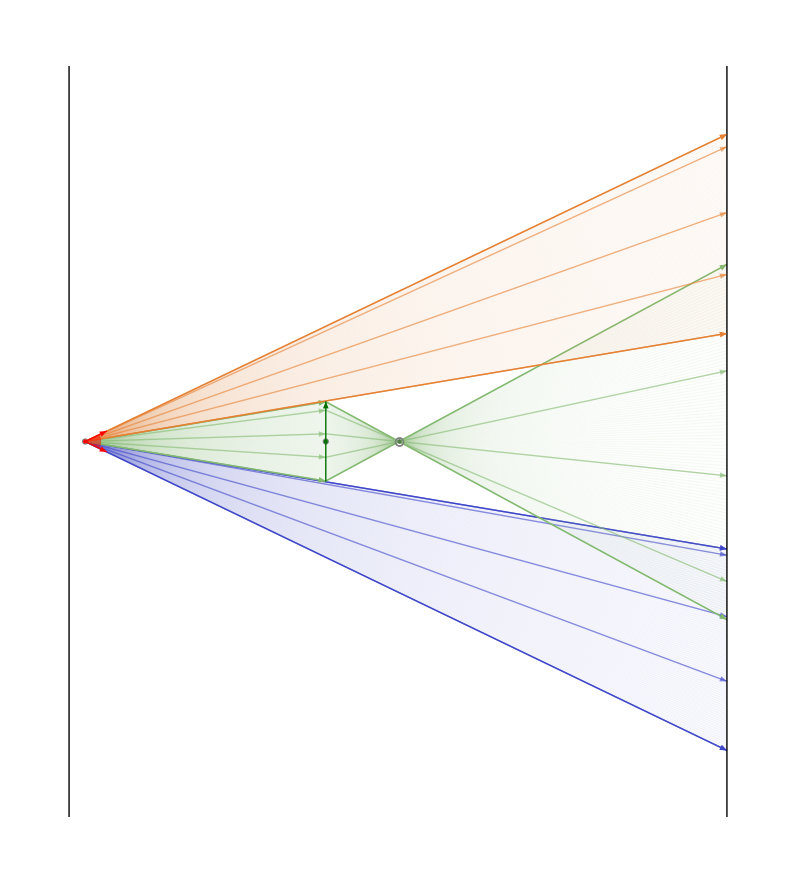

```mathematica
all={source["point",{0,0},0,Pi/7,N[Pi/1000]],lens[{{3,-.5},{3,.5}},.7]};
completedraw[all,{{-.2,8},{-5,5}},{{-.15,8},{-4.5,4.5}}]
```

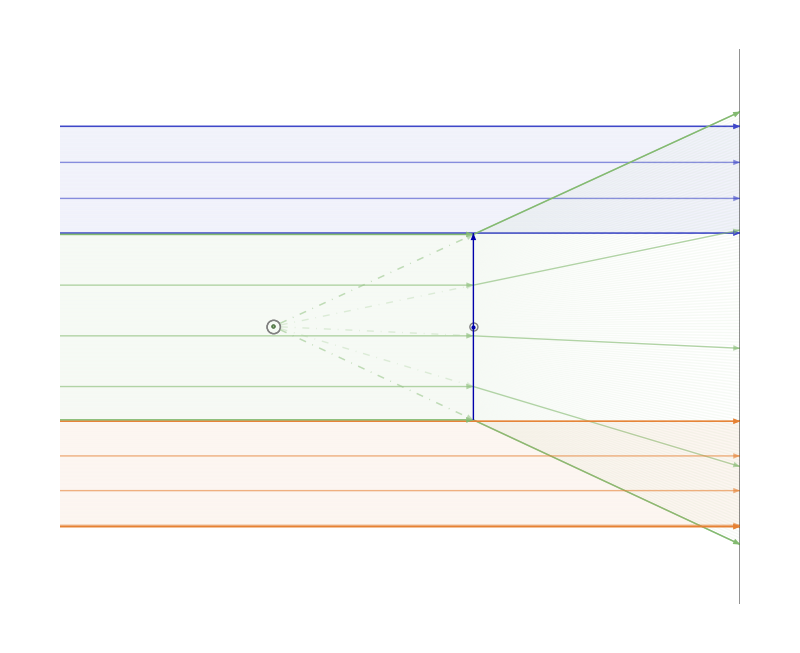

```mathematica
all={source["line",{{-2,-1.5},{-2,1.5}},0,0.01],lens[{{3,-.7},{3,.7}},-1.5]};
completedraw[all,{{-2.1,5},{-10,10}},{{0,4.9},{-2,2}}]
```

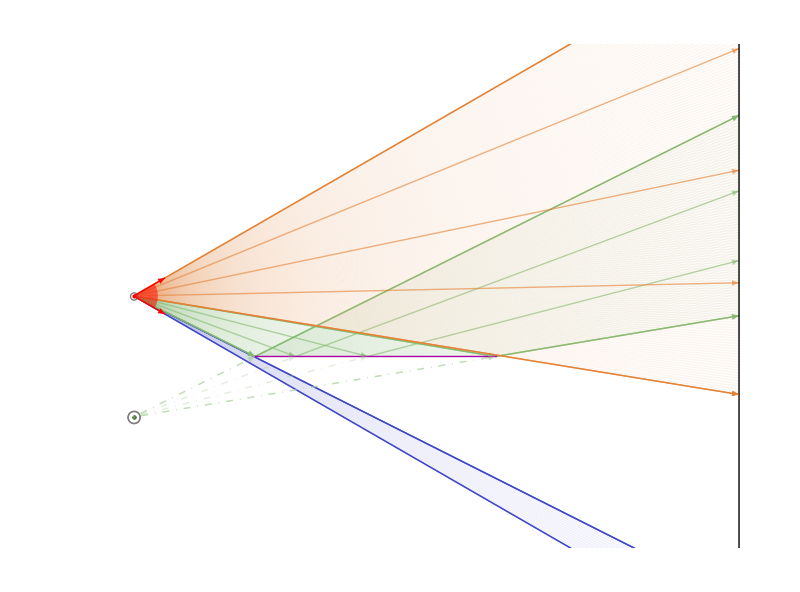

```mathematica
all={source["point",{0,0},0,Pi/6],onlymirror[{{1,-.5},{3,-.5}}]};
completedraw[all,{{-1,5},{-3,3}},{{-.5,4.9},{-2,2}}]
```

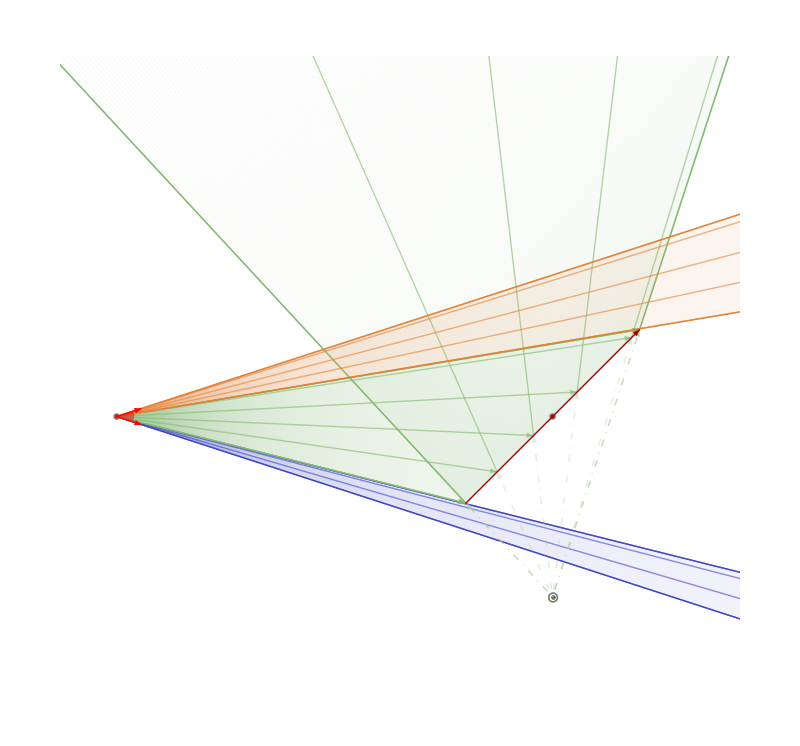

```mathematica
all={source["point",{0,0},0,Pi/10,N[Pi/2000]],mirror[{{4,-1},{6,1}},1/2,-5]};
completedraw[all,{{-3,8},{-4,5}},{{-.5,7},{-3,4}}]
```

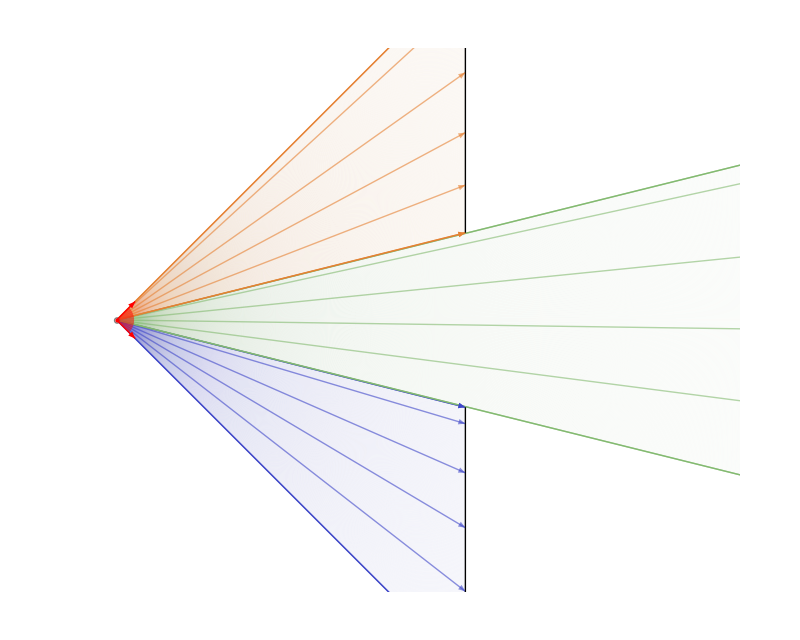

```mathematica
all={source["point",{0,0},0,Pi/4,N[Pi/2000]],doubleaper[{{4,-1},{4,1}}]};
completedraw[all,{{-3,8},{-4,5}},{{-.5,7},{-3,3}}]
```

#### Double Mirror

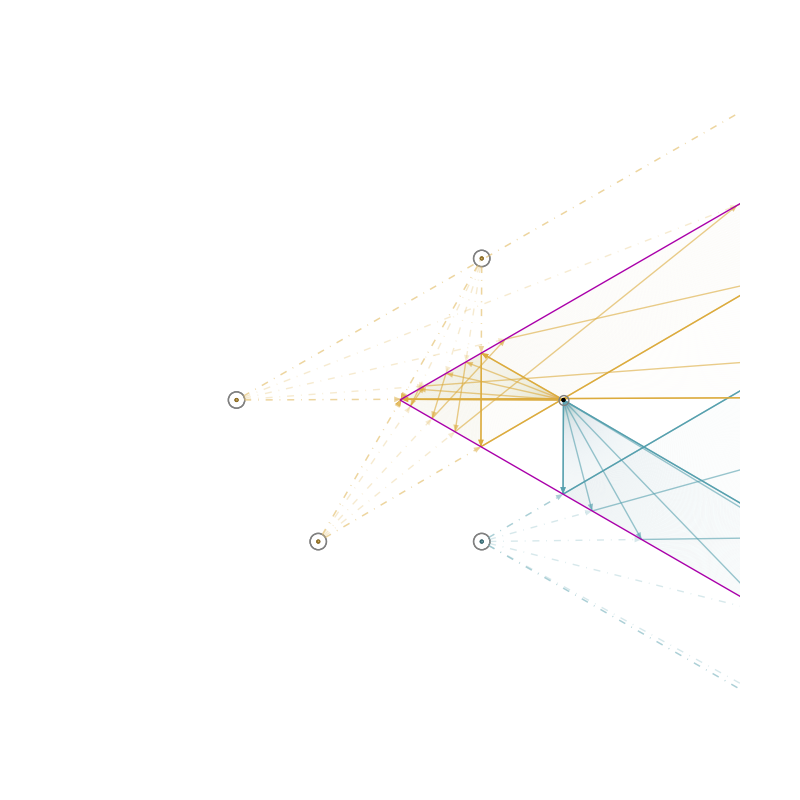

```mathematica
all={source["point",{1,0},0,Pi,N[Pi/1440]],onlymirror[{{0,0},{100,100/Sqrt[3]}}],onlymirror[{{0,0},{100,-100/Sqrt[3]}}]};
completedraw[all,{{-3,100},{-100,100}},{{-2,2},{-2,2}}]
```

#### Telescope

```mathematica
all={source["line",{{10,-2},{10,1.3}},Pi+Pi/100,0.02],source["line",{{10,-1.3},{10,2}},Pi-Pi/100,0.02],source["line",{{10,-0.99},{10,0.99}},Pi,0.02],lens[{{5,-2},{5,2}},5],lens[{{-1,-0.2},{-1,0.2}},1]};
completedraw[all,{{-4.1,11},{-4,4}},{{-4,8},{-2,2}}]
```

-Graphics-

```mathematica
all={source["line",{{10,-2},{10,1.3}},Pi+Pi/100,0.02],source["line",{{10,-1.3},{10,2}},Pi-Pi/100,0.02],source["line",{{10,-0.99},{10,0.99}},Pi,0.02],lens[{{5,-2},{5,2}},5],lens[{{1,-0.2},{1,0.2}},-1]};
completedraw[all,{{-2.1,11},{-4,4}},{{-2,8},{-2,2}}]
```

-Graphics-

```mathematica
all={source["line",{{10,-3},{10,3}},Pi+Pi/300,0.02],source["line",{{10,-3},{10,3}},Pi-Pi/300,0.02],source["line",{{10,-3},{10,3}},Pi,0.02],
mirror[{{0,-2.5},{0,2.5}},10],mirror[{{6,-.3},{6,.3}},2],onlymirror[{{1.7,-.3},{2.3,.3}}],
aperture[{{6.01,-.31},{6.01,.31}}]};
completedraw[all,{{-2.1,11},{-7.1,3.1}},{{-2,8},{-7,3}}]
```

-Graphics-

#### Magnifier

```mathematica
all={source["point"],source["point",{0,.25}],lens[{{2,-.7},{2,.7}},3]};
completedraw[all,{{-5.1,4},{-2,2}},{{-5,4},{-1.5,1.5}}]
```

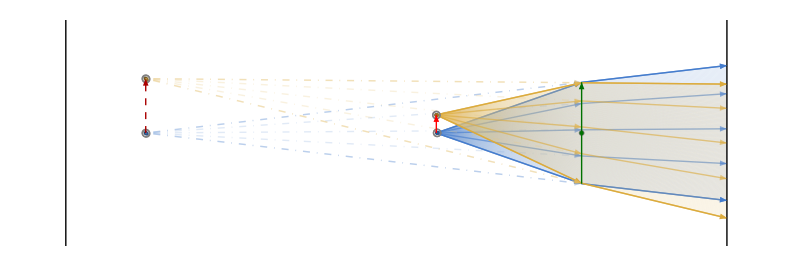

```mathematica
Show[img,Graphics[{Red,Arrowheads@Medium,Arrow[{{0,0},{0,.25}}],Darker@Red,Dashed,Arrow[{{-4,0},{-4,.75}}]}]]
```

#### Microscope

```mathematica
all={source["point",{0,0},0,Pi/2],source["point",{0,.15},0,Pi/2],lens[{{1,-1},{1,1}},0.75],lens[{{5,-1.5},{5,1.5}},1.2]};
completedraw[all,{{-3,10},{-4,4}},{{-2,10},{-3,3}}]
```

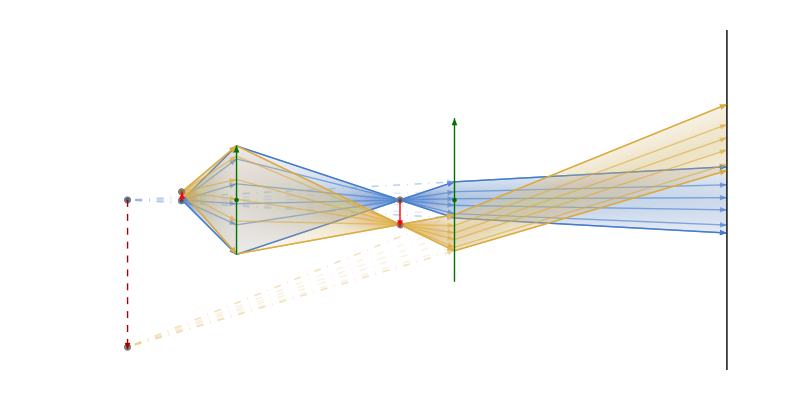

```mathematica
Show[img,
Graphics[{Red,Arrowheads@Medium,Arrow[{{0,0},{0,0.15}}],Arrow[{{4,0},{4,-0.5}}],Darker@Red,Dashed,Arrow[{{-1,0},{-1,-2.75}}]}]]
```

## Testing Area

```mathematica
all={source["point"],traverse[{{0.99,-.5},{.99,.5}},{.01,0}]};
completedraw[all]
```

```mathematica
Table[Graphics[{Line[{{0,0},{x,0}}]},Frame->True],{x,1.*^9,1.*^10,1.*^9}]
```

```mathematica
all={source["point",{0,.1}],source["point",{0,-.1}],lens[{{3,-.5},{3,.5}},.7]};
completedraw[all,{{-.2,8},{-5,5}},{{-.15,8},{-4.5,4.5}}]
```